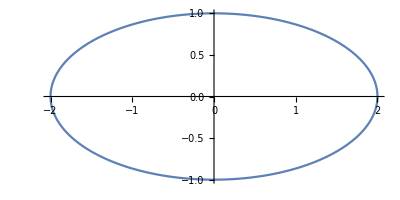

-Graphics3D-

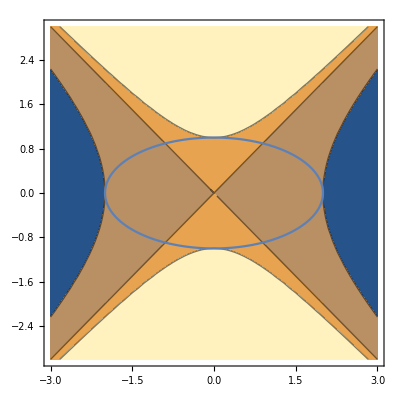

```mathematica
g1=Plot3D[{y^2-x^2},{x,-3,3},{y,-3,3},PlotStyle->Directive[Orange,Specularity[White,50],Opacity[0.5]]];
g2=ParametricPlot3D[{2*Cos[u],Sin[u],t},{u,0,2*Pi},{t,-6,6},PlotStyle->Directive[Green,Specularity[White,50],Opacity[0.8]]];
g3=ContourPlot[{y^2-x^2},{x,-3,3},{y,-3,3},Contours->{-4,0,1}];
g4=ParametricPlot[{2*Cos[u],Sin[u]},{u,0,2*Pi}]
Show[g1,g2]
Show[g3,g4]
```

-Graphics3D-

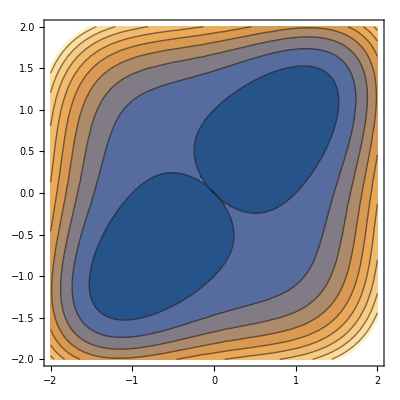

```mathematica
Plot3D[{y^4+x^4-x^2-2x*y-y^2},{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,50],Opacity[0.5]]]
ContourPlot[{y^4+x^4-x^2-2x*y-y^2},{x,-2,2},{y,-2,2}]
```

```mathematica
ParametricPlot3D[{Cos[u],Sin[u],t},{u,0,2*Pi},{t,-3,3},PlotStyle->Directive[Green,Specularity[White,50],Opacity[0.8]]]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[1-x^2-y^2],{x,-1,1},{y,-1,1},Filling->Bottom,Ticks->None,BoundaryStyle->Black,AxesLabel->{x,y,z},PlotStyle->Opacity[1]]
```

-Graphics3D-

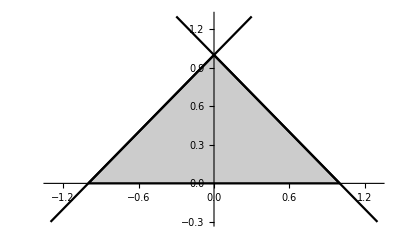

```mathematica
f[x_]:=1-x;g[x_]:=1+x;
Quxian1=Plot[f[x],{x,-0.3,1.3},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quxian2=Plot[g[x],{x,-1.3,0.3},AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu1=Plot[{0,f[x]},{x,0,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Quyu2=Plot[{0,g[x]},{x,-1,0},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black];
Show[Quyu1,Quyu2,Quxian1,Quxian2]
```

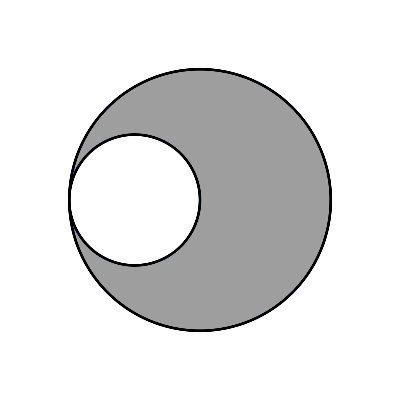

```mathematica
Quxian1=PolarPlot[2Cos[t],{t,0,2Pi},PlotStyle->Black,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}];
Quxian2=PolarPlot[4Cos[t],{t,0,2Pi},PlotStyle->Black,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}];
Quyu=RegionPlot[(x-1)^2+y^2>=1&&(x-2)^2+y^2<=4,{x,-1,5},{y,-3,3},PlotStyle->GrayLevel[.618],Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}];
Show[Quyu,Quxian1,Quxian2,PlotRange->{{-0.5,4.5},{-2.5,2.5}},AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,Ticks->{{-2,-1,0,1,2},{-2,-1,0,1,2}}]
```

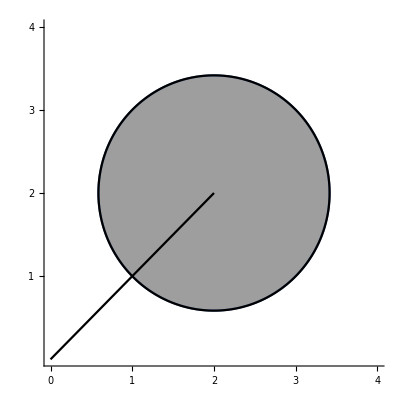

```mathematica
C1=ParametricPlot[{Sqrt[2]Cos[t]+2,Sqrt[2]Sin[t]+2},{t,0,2Pi},PlotStyle->Black];
C2=RegionPlot[(x-2)^2+(y-2)^2≤2,{x,0,4},{y,0,4},PlotStyle->GrayLevel[.618],AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False,PlotRange->{{0,4},{0,4}},Ticks->{{0,1,2,3,4},{1,2,3,4}}];
L=Plot[x,{x,0,2},PlotStyle->Black,AxesStyle->Arrowheads[0.04],Axes->Automatic,AspectRatio->1,Frame->False];
Show[C2,C1,L]
```

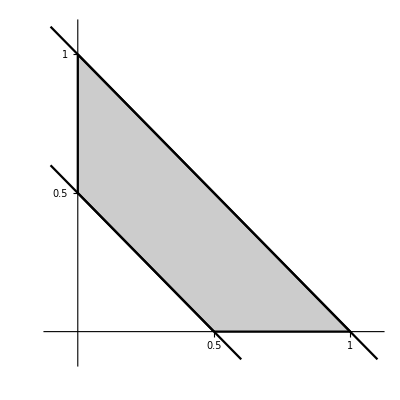

```mathematica
f[x_]:=1-x;g[x_]:=1/2-x;
Quxian1=Plot[f[x],{x,-0.1,1.1},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quxian2=Plot[g[x],{x,-0.1,0.6},AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quyu1=Plot[{g[x],f[x]},{x,0,0.5},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1,Ticks->{{0.5,1},{0.5,1}}];
Quyu2=Plot[{0,f[x]},{x,0.5,1},Filling->{1->{2}},PlotRange->All,AxesStyle->Arrowheads[0.04],PlotStyle->Black,AspectRatio->1];
LX0=ParametricPlot[{0,y},{y,0.5,1},PlotStyle->Black,PlotStyle->Black];
Show[Quyu1,Quyu2,Quxian1,Quxian2,LX0]
```